```mathematica
ClearAll["Global`*"]

logSpace[start_,end_,num_]:=10^Range[start,end,(end-start)/(num-1)]

dir=NotebookDirectory[];
matrixFiles=FileNames["matrix_*.mx",dir];
matrices=Import/@matrixFiles;

wvals = SetPrecision[logSpace[-21,-17,Length[matrices]] ,150];
```

```mathematica
For[i = 1,i<Length[matrices]+1,i++,
Print[(matrices[[i,1,2]]^2 )/(matrices[[i,1,2]]^2 + matrices[[i,1,1]]^2)]
]
```

0.5006218129946880773

0.5006109752064611517

0.50056187138295318

0.5003595733930725388

0.5006248051911620979

0.5006248051802531129

0.5006248051296180915

0.5006248048945911671

0.5006248038036933782

0.5006247987402064228

0.5006247752378413062

0.5006246661551142829

0.5006241599583438381

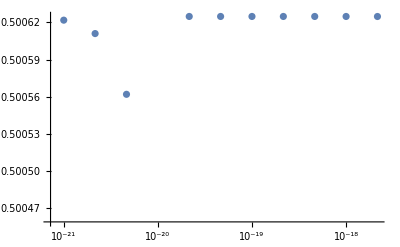

```mathematica
data = Table[
{wvals[[i]],(matrices[[i,1,2]]^2 )/(matrices[[i,1,2]]^2 + matrices[[i,1,1]]^2)},{i,1,Length[matrices]}
];
ListPlot[data,ScalingFunctions->{"Log",None},GridLinesStyle->Red]
```

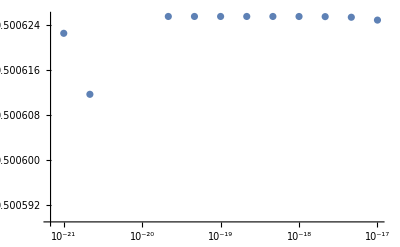

```mathematica
data = Table[
{wvals[[i]],
(Sum[matrices[[i,1,j]]^2,{j,2,Length[matrices[[1,1]]]}] )/(Sum[matrices[[i,1,j]]^2,{j,2,Length[matrices[[1,1]]]}] + matrices[[i,1,1]]^2)},{i,1,Length[matrices]}
];
ListPlot[data,ScalingFunctions->{"Log",None},GridLinesStyle->Red]
```